```mathematica
Question no 6

(a)
```

```mathematica
f[x_] = Sin[(π x)/2];
g[x_] = x^2 - 2x;
```

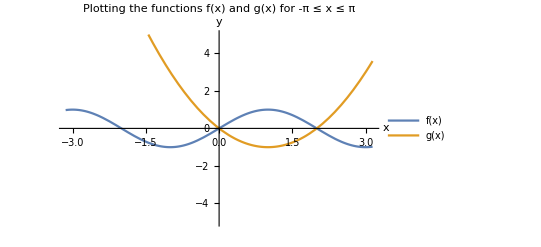

```mathematica
Plot[{f[x], g[x]}, {x, -π, π},
(*plotting options*)
AxesLabel->{"x", "y"},
PlotLabel->"Plotting the functions f(x) and g(x) for -π ≤ x ≤ π",
PlotStyle->Thick,
PlotRange->{-5, 5},
PlotLegends->"Expressions"]
```

```mathematica
(b)
```

```mathematica
Solve[f[x] == g[x]  && −π≤x≤π, x]
```

{{x→0},{x→2}}

```mathematica
(c)
```

```mathematica
∫_0^2 ( f[x] - g[x] )ⅆx  // N
```

2.60657